```mathematica
(*data1 is in pairs of current and frequency; voltage goes from
0 to 8.06 volts, frequency goes from 40.676Hz to 42.382Hz; this is experimental data *)
data1={{0, 40.676}, {.097, 41.108}, {.2,41.563}, {.299,41.985},{.394, 42.382}}
```

{{0,40.676},{0.097,41.108},{0.2,41.563},{0.299,41.985},{0.394,42.382}}

```mathematica
(*freq0 -> frequency with no applied current*)
freq0= 40.676; 

dfreqdi= 4.154;(*the change with frequency*)

(*The "RandomVariate[NormalDistribution]" creates points based on "freq0" and "dfreqi" forming data points similar to the experimental data *)
data2 = Table[{x,freq0+dfreqdi*x+.01*RandomVariate[NormalDistribution[]]},     {x,0,.4,.04}]
```

{{0.,40.6763},{0.04,40.8168},{0.08,41.0182},{0.12,41.1787},{0.16,41.3406},{0.2,41.4974},{0.24,41.6664},{0.28,41.8454},{0.32,42.0207},{0.36,42.1583},{0.4,42.3433}}

```mathematica
(*Data ranges are are slightly lower except for the minimum 
data pointand slightly higher for the maximum data point *)
```

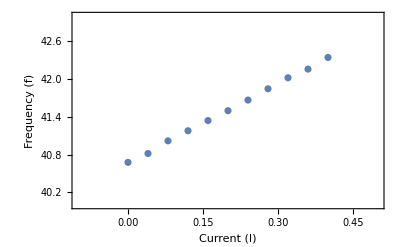

```mathematica
ListPlot[data2,PlotRange->{{-0.1,0.5},{40,43}}, Frame->True,FrameLabel->{"Current (I)","Frequency (f)"}]
```

```mathematica
fitline = linearModelFit[data2,{1,x},x]
```

linearModelFit[{{0.,40.6763},{0.04,40.8168},{0.08,41.0182},{0.12,41.1787},{0.16,41.3406},{0.2,41.4974},{0.24,41.6664},{0.28,41.8454},{0.32,42.0207},{0.36,42.1583},{0.4,42.3433}},{1,x},x]

```mathematica
fitline["ParameterTable"]
```

linearModelFit[{{0.,40.6763},{0.04,40.8168},{0.08,41.0182},{0.12,41.1787},{0.16,41.3406},{0.2,41.4974},{0.24,41.6664},{0.28,41.8454},{0.32,42.0207},{0.36,42.1583},{0.4,42.3433}},{1,x},x][ParameterTable]

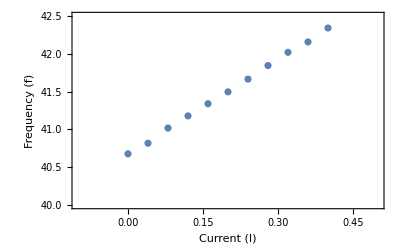

```mathematica
Show[ListPlot[data2, PlotRange->{{-0.1,0.5}, {40,42.5}}, Frame->True,FrameLabel->{"Current (I)", "Frequency (f)"}],Plot[fitline[x],{x,-1,3}]]
```

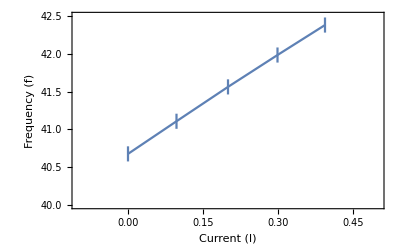

```mathematica
Needs["ErrorBarPlots`"]

(*Error plot mreated from "data1" data array with connected points*)

ErrorListPlot[{{{0, 40.676},ErrorBar[0.1]}, {{.097, 41.108},ErrorBar[0.1]}, {{.2,41.563},ErrorBar[0.1]}, {{.299,41.985},ErrorBar[0.1]},{{.394, 42.382},ErrorBar[0.1]}},Frame->True,FrameLabel->{"Current (I)", "Frequency (f)"},PlotRange-> {{-0.1,0.5}, {40,42.5}}, Joined -> True]
```

```mathematica
(*Error plot mreated from "data2" data array with connected points*)
```

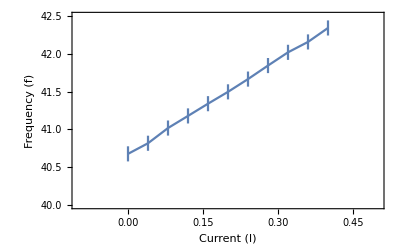

```mathematica
ErrorListPlot[{{{0.0,40.676287169713355},ErrorBar[0.1]},{{0.04,40.8167641571114},ErrorBar[0.1]},{{0.08,41.01818137156022},ErrorBar[0.1]},{{0.12,41.17867006468222},ErrorBar[0.1]},{{0.16,41.34056262680236},ErrorBar[0.1]},{{0.2,41.49739530112882},ErrorBar[0.1]},{{0.24,41.666397281449015},ErrorBar[0.1]},{{0.28,41.845448190786094},ErrorBar[0.1]},{{0.32,42.02066988884834},ErrorBar[0.1]},{{0.36,42.158260384911436},ErrorBar[0.1]},{{0.4,42.3433231673125},ErrorBar[0.1]}},Frame->True,FrameLabel->{"Current (I)", "Frequency (f)"},PlotRange-> {{-0.1,0.5}, {40,42.5}}, Joined -> True]
```